```mathematica
<<AtomicDensityMatrix`
```

## Toy model 1

#### Level structure

Consider a model where a laser drives transitions between the electronic ground and excited states. The excited state has J'=1 and has a lifetime of about 100 ns. In the ground state, only decays/transitions to J=0 and J=2 are allowed. 

-Graphics-

#### Branching ratios

Take the expression for unnormalized matrix elements from Hutzler’s eqn 2.57:

```mathematica
ME[J_,M_,Ω_,Jp_,Mp_,Ωp_]:=(2J+1)(2Jp+1)ThreeJSymbol[{J,-Ω},{1,Ω-Ωp},{Jp,Ωp}]^2 ThreeJSymbol[{J,-M},{1,M-Mp},{Jp,Mp}]^2
```

Then the branching ratios are

```mathematica
b2=Sum[
ME[2,M,0,1,Mp,1],
{M,-2,2},
{Mp,-1,1}
];
b0=Sum[
ME[0,M,0,1,Mp,1],
{M,0,0},
{Mp,-1,1}
];
```

ClebschGordan::phy: ThreeJSymbol[{2,2},{1,-2},{1,0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2,2},{1,-3},{1,1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2,1},{1,-2},{1,1}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

Normalized, this is

```mathematica
b2/(b0+b2)
b0/(b0+b2)
```

1/3

2/3

The normalized branching ratios to individual M_J states are

```mathematica
b[J_,M_]:=1/(b0+b2)Sum[ME[J,M,0,1,Mp,1],{Mp,-1,1}]
```

```mathematica
Table[
Table[b[J,M],{M,-J,J}],
{J,{0,2}}
]
```

ClebschGordan::phy: ThreeJSymbol[{2,2},{1,-2},{1,0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2,2},{1,-3},{1,1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2,1},{1,-2},{1,1}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

{{2/3},{1/15,1/15,1/15,1/15,1/15}}

#### Liouville equations

Setup the system:

```mathematica
system=Sublevels[{
AtomicState[0,NaturalWidth->0,Energy->0,J->0],
AtomicState[2,NaturalWidth->0,Energy->Δ,J->2],
AtomicState["e",NaturalWidth->Γ,BranchingRatio[0]->2/3,BranchingRatio[2]->1/3,J->1]
}];
```

Add the σ^sgn, sgn=+/-, laser field:

```mathematica
laser={{
ElectricField->OpticalField[ω,Ω/ReducedME[2,{Dipole,1},"e"],{0,sgn π/4}],
RestrictCoupling->{2->"e"}
}};
```

This looks as following, depending on the choice of sgn:

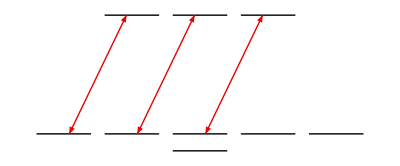

```mathematica
LevelDiagram[system,Hamiltonian[system,laser]/.Δ->.25/.δ->0/.sgn->1]
```

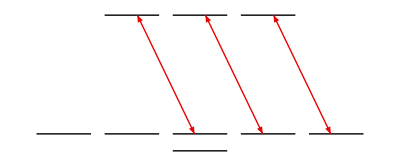

```mathematica
LevelDiagram[system,Hamiltonian[system,laser]/.Δ->.25/.δ->0/.sgn->-1]
```

Find the Hamiltonian in the rotating wave approximation:

```mathematica
Hrwa=RotatingWaveApproximation[
system,Hamiltonian[system,laser],
{{ω,2->"e",δ}}
];
```

The equations of motion are:

```mathematica
eqs=LiouvilleEquation[
system,
Hrwa,
relax=IntrinsicRelaxation[system],
repop=OpticalRepopulation[system]
];
```

#### Solving the equations

For σ^+ light, the solution behaves as

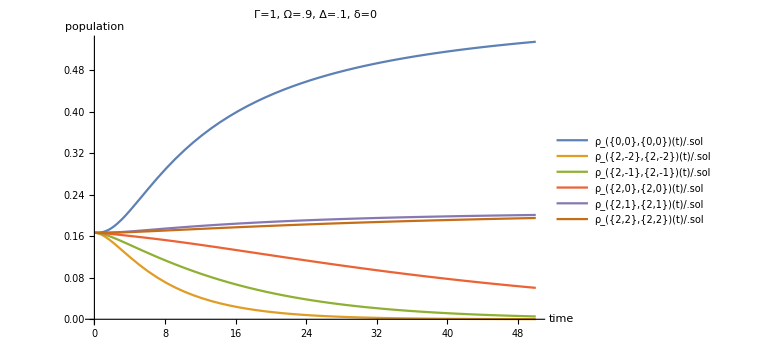

```mathematica
sol=NDSolve[
Join[
eqs/.Γ->1/.Ω->.9/.Δ->.1/.δ->0/.sgn->1,
InitialConditions[system,({{1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}})/6,0]
],DMVariables[system],{t,0,50}
];
Plot[
{
Subscript[ρ, {0,0},{0,0}][t]/.sol,
Subscript[ρ, {2,-2},{2,-2}][t]/.sol,
Subscript[ρ, {2,-1},{2,-1}][t]/.sol,
Subscript[ρ, {2,0},{2,0}][t]/.sol,
Subscript[ρ, {2,1},{2,1}][t]/.sol,
Subscript[ρ, {2,2},{2,2}][t]/.sol
},
{t,0,50},
PlotLegends->"Expressions",
PlotLabel->"Γ=1, Ω=.9, Δ=.1, δ=0",
AxesLabel->{"time","population"},
BaseStyle->{FontSize->16},
ImageSize->Large
]
```

If we switch between σ^+ and σ^- at a certain rate, it looks like

```mathematica
switchingTime=50;
sol=NDSolve[
Join[
eqs/.Γ->1/.Ω->.9/.Δ->.1/.δ->0/.sgn->(-1)^Round[t/switchingTime],
InitialConditions[system,({{1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}})/6,0]
],DMVariables[system],{t,0,160}
];
```

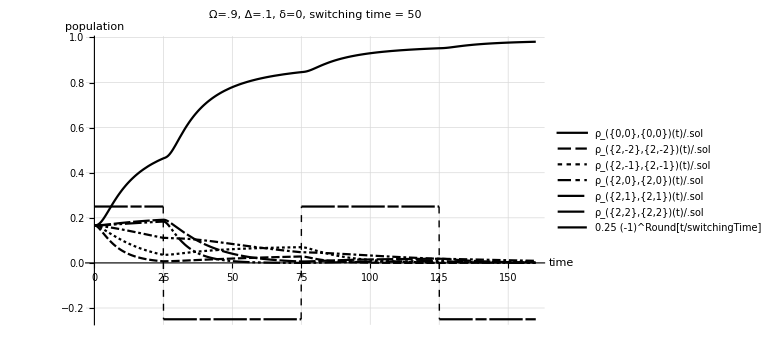

```mathematica
plt0=Plot[
{
Subscript[ρ, {0,0},{0,0}][t]/.sol,
Subscript[ρ, {2,-2},{2,-2}][t]/.sol,
Subscript[ρ, {2,-1},{2,-1}][t]/.sol,
Subscript[ρ, {2,0},{2,0}][t]/.sol,
Subscript[ρ, {2,1},{2,1}][t]/.sol,
Subscript[ρ, {2,2},{2,2}][t]/.sol,
.25(-1)^Round[t/switchingTime]
},
{t,0,160},
PlotLegends->"Expressions",
PlotLabel->"Ω=.9, Δ=.1, δ=0, switching time = 50",
AxesLabel->{"time","population"},
ImageSize->Large,
PlotRange->All,
ExclusionsStyle->Dashed,
PlotTheme->"Monochrome",
BaseStyle->FontSize->16,
GridLines->Automatic
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["switching.pdf",plt0]
```

/home/jk/temp/thesis/figs/mathematica

switching.pdf

Let’s consider the ground-state population at t=50 as a measure of how efficiently we’re depleting the J=2 state. As a function of switching time (more time = slower switching), this looks like

```mathematica
res=Table[
Subscript[ρ, {0,0},{0,0}][t]/.NDSolve[
Join[
eqs/.Γ->1/.Ω->.9/.Δ->.1/.δ->0/.sgn->(-1)^Round[t/switchingTime],
InitialConditions[system,({{1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}})/6,0]
],DMVariables[system],{t,0,50}
]⟦1⟧/.t->50//Chop,
{switchingTime,1,100,1}
];
```

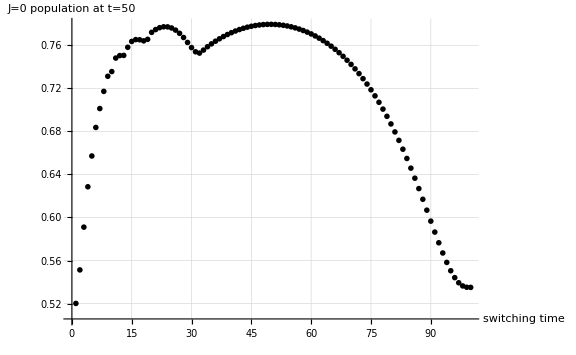

```mathematica
plt1=ListPlot[res,
AxesLabel->{"switching time", "J=0 population at t=50"},
PlotTheme->"Monochrome",
BaseStyle->FontSize->16,
GridLines->Automatic,
PlotStyle->Black
]
```

Seems like 25 is the optimal switching time. Let’s similarly optimize laser power:

```mathematica
res2=Table[
{Ω,Subscript[ρ, {0,0},{0,0}][t]/.NDSolve[
Join[
eqs/.Γ->1/.Δ->.1/.δ->0/.sgn->(-1)^Round[t/25],
InitialConditions[system,({{1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}})/6,0]
],DMVariables[system],{t,0,50}
]⟦1⟧/.t->50//Chop},
{Ω,0,2,.1}
];
```

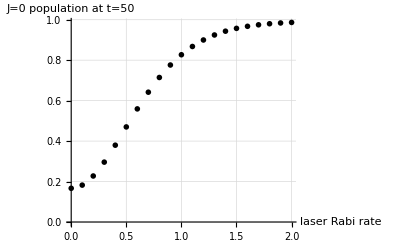

```mathematica
plt2=ListPlot[res2,
AxesLabel->{"laser Rabi rate", "J=0 population at t=50"},
PlotTheme->"Monochrome",
BaseStyle->FontSize->16,
GridLines->Automatic,
PlotStyle->Black
]
```

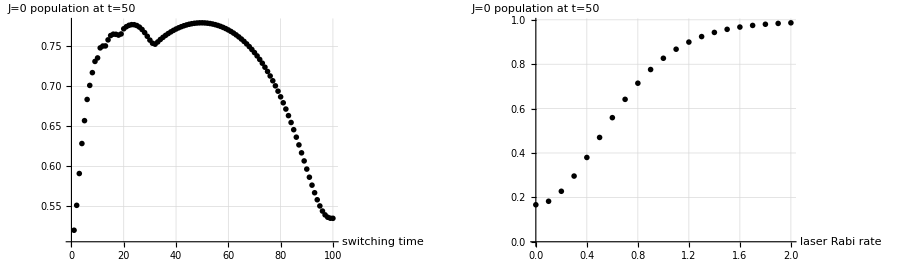

```mathematica
pl=GraphicsGrid[{{plt1,plt2}},ImageSize->900]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["RC_sw_time.pdf",pl]
```

/home/jk/temp/thesis/figs/mathematica

RC_sw_time.pdf